# MonteCarlo.m

## marcel.utz@gmx.net January 2018

```mathematica
MCMacroStep[F_Symbol,q_,scale_,T_] :=
Module[ {l=Length[q],E0=F[q]},
qnew=q+scale*RandomReal[{-0.5,0.5},l];
Enew=F[qnew];
If[Enew-E0<0 || Exp[Enew-E0]/T < RandomReal[],
{ qnew, Enew,True},
{ q, E0, False}
] 
]
```

### Himmelblau’s Function

This is a slightly modified version of Himmelblau’s function. The last term (-10 x y) is added to ensure that the minima are not at the same depth.

```mathematica
HimmelBlau[{x_,y_}] :=  (x^2+y-11)^2+(x+y^2-7)^2-10 x y
```

```mathematica
hbp=Plot3D[HimmelBlau[{x,y}],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
q0={0.,0.} ;
scale={0.2,0.2};
traj={};
CoolRate=0;
T0=2000;
nsteps=100000;
traj=ConstantArray[{q0,0.0,False},nsteps];
q=q0;
Timing[Do[
{q,enew,accept}=MCMacroStep[HimmelBlau,q,scale,T0 Exp[CoolRate k/nsteps]];
traj[[k]]={q,enew,accept};,
{k,1,nsteps}
];]
```

{23.7939,Null}

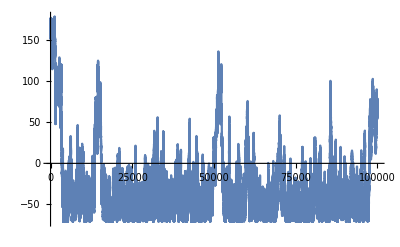

-Graphics3D-

```mathematica
ListLinePlot[traj[[;;,2]] , PlotRange->All]
Show[hbp,Graphics3D[Line[traj /. {{x_,y_},en_,_}->{x,y,en}]]]
```